# BigData Optimal Tax: Life-Cycle

This notebook takes the basic life cycle model and examines what happens for many alternative combinations of capital and labor tax rates.

```mathematica
x=0; Remove["Global`*"];
```

Define the main life-cycle constants, the utility function, and the age-wage path.

```mathematica
Needs["IPOPTLink`"]
```

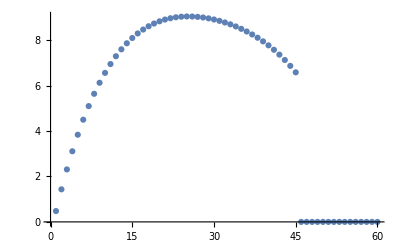

```mathematica
T=60;Tret=45;
r=0.1;R=1 + r; 
β=.95;
u[c_,l_] :=c^(1-γ)/(1-γ)-B l^(1+η)/(1+η)
Clear[w];
(* Specify age-wage path*)
Do[w[t]=-36.9994+3.52022(t+17)-.101878(t+17)^2+.00134816(t+17)^3-7.06233*10^-6(t+17)^4,{t,1,Tret}];
wagelist=Table[If[i≤ Tret,w[i],0],{i,T}];
ListPlot[wagelist]
```

We define the basic optimization problem.

```mathematica
Tax[capInc_,labInc_]:=τK (R-1) capInc   +τL labInc;
PVrevL:= Sum[τL w[t] l[t] R^(-t+1),{t,1,Tret}] ;
PVrevK:= Sum[τK (R-1) a[t] R^(-t+1),{t,1,T}] ;
PVrevC:= Sum[τC c[t] R^(-t+1),{t,1,T}] ;
```

```mathematica
obj := Sum[β^(t-1) u[c[t],l[t]],{t,1,T}];
(*Define Budget Constraints*)
bc1:=Table[(R  a[t]+w[t] l[t]-c[t]-Tax[ a[t],w[t] l[t]])-a[t+1]≥ 0,{t,1,T}];
(*Define bound Constraints*)
bcaT:={a[T+1]≥ 0};
abnds:=Table[a[t]≥ amin,{t,2,T}];
lbndsc:=Table[c[t]≥ 0.0001,{t,2,T}];
lbndsl:=Map[#≥0&,Table[l[t],{t,1,Tret}]]; 
{vars,varbounds} = (Union[abnds,bcaT,lbndsc,lbndsl ]/.{( a_≥ b_  ) -> {a,b,∞}}//Transpose)/. {v_,lb_,ub_}:> {v,Transpose[{lb,ub}]};

ipoptConstraintStyle= 
{
	( a_== b_  ) -> LessEqual[0,a-b,0],
	( a_ <=  b_ ) -> LessEqual[-∞,a-b,0],
	(a_ >= b_  ) -> LessEqual[0,a-b,∞]
};
{budgetconstraintfunctions,budgetconstraintvals} = Transpose[bc1 /.ipoptConstraintStyle/. LessEqual[lb_,v_,ub_]-> {v,{lb,ub}} ];
```

```mathematica
(*Set initial guess for all variables to be 1; probably not a feasible point but better than letting them be zero.*)
varsinit=Table[1,Length[vars]];
```

```mathematica
(*Define border conditions particular to the problem*)
a[1]=0;
Do[ l[i]=0,{i,Tret+1,T}];
c[1] = 0.01
```

0.01

```mathematica
pfunc = ParametricIPOPTMinimize[-obj,
						vars,
						Table[start[i],{i,1,Length[vars]}],
						varbounds,
						budgetconstraintfunctions,
						budgetconstraintvals,
						Join[Table[start[i],{i,1,Length[vars]}],{τK,τL,amin,γ,η,B}]];
```

This is the command which takes as input the tax rates, the borrowing constraints, and preference parameters, and outputs the individuals utility and solution path.

NOTE: This is a very simple problem. One should think of f[----] as a black box because it will often be a substantive computation on its own. In this notebook I do nothing that relies on special features of this problem. I use this problem because it is fast to compute, and it allows me to demonstrate the general concept of computing a Pareto frontier.

```mathematica
f[initialguess_,params_]:=
Block[{a,c,l,utility,PVrevK0,PVrevL0,τK0,τL0,amin0,γ0,η0,B0},
{τK0,τL0,amin0,γ0,η0,B0}=params;
ipoptOut = pfunc[Sequence@@Join[initialguess,{τK0,τL0,amin0,γ0,η0,B0}]];
sol = IPOPTArgMin[ipoptOut];
utility = -IPOPTMinValue[ipoptOut];
Sow[{utility,sol,τK0,τL0}];
sol
];
(*(f[initialguess_,b_] :=Block[{utility,c},pfunc[Sequence@@Join[initialguess,{0.4,0.5,-3000,0.5,1,1}]]])*)
```

Here is a simple example

```mathematica
(*ipoptOut = pfunc[Sequence@@Join[varsinit,{.4,.5,-3000,0.5,1,1}]];
sol = IPOPTArgMin[ipoptOut];
utility = -IPOPTMinValue[ipoptOut];
{utility,sol,τK0,τL0}*)
(*asdf = f[varsinit,{.4,.5,-3000,0.5,1,1}]*)
Reap[f[varsinit,{.4,.5,-3000,0.5,1,1}]][[2]]
(*IPOPTArgMin[asdf]
-IPOPTMinValue[asdf]*)
(*//AbsoluteTiming*)
```

{{{60.9717,{0.0187367,-3.70187,-7.29556,-10.6307,-13.6107,-16.1681,-18.2594,-19.8604,-20.9623,-21.5685,-21.6919,-21.3521,-20.5739,-19.3857,-17.8176,-15.9011,-13.6676,-11.1484,-8.37369,-5.37254,-2.17262,1.19988,4.7203,8.36543,12.1134,15.9435,19.836,23.772,27.733,31.7011,35.6579,39.5851,43.4639,47.2745,50.9962,54.6071,58.0838,61.4012,64.5327,67.4496,70.1216,72.5165,74.6004,76.3381,77.6935,75.0032,72.0483,68.8114,65.274,61.4167,57.2187,52.6581,47.7115,42.3543,36.5602,30.3013,23.5481,16.2693,8.4317,1.44653×10^-7,3.97926,4.03516,4.09185,4.14934,4.20763,4.26675,4.32669,4.38748,4.44912,4.51162,4.57501,4.63928,4.70446,4.77055,4.83757,4.90554,4.97445,5.04434,5.11521,5.18707,5.25994,5.33384,5.40878,5.48476,5.56182,5.63996,5.71919,5.79954,5.88102,5.96364,6.04743,6.13239,6.21854,6.3059,6.3945,6.48433,6.57543,6.66781,6.76148,6.85648,6.9528,7.05048,7.14954,7.24998,7.35183,7.45512,7.55986,7.66607,7.77377,7.88298,7.99373,8.10603,8.21991,8.33539,8.4525,8.57125,8.69167,8.81377,8.9376,0.120443,0.359303,0.574756,0.768438,0.941904,1.09663,1.23402,1.35539,1.46201,1.55505,1.63562,1.70478,1.76351,1.81272,1.85327,1.88597,1.91154,1.93069,1.94402,1.95212,1.95552,1.95468,1.95004,1.94197,1.9308,1.91683,1.90029,1.8814,1.86031,1.83716,1.81203,1.78498,1.75601,1.72511,1.69224,1.65731,1.62021,1.58079,1.5389,1.49433,1.44685,1.39623,1.34219,1.28443,1.22264},0.4,0.5}}}

```mathematica
f[Sequence@@Join[varsinit,{.4,.5,-3000,0.5,1,1}]]
```

f[1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.4,0.5,-3000,0.5,1,1]

## Create Database

Build your database (or import it if already built)

```mathematica
gamlist={1/2};
etalist={1};
```

```mathematica
tkmax=0.4; tlmax=0.4;
```

```mathematica
dtk=0.05; dtl=0.05;
```

```mathematica
ntk=tkmax/dtk+1
ntl=tlmax/dtl + 1
```

9.

9.

We next evaluate many combinations of taxes for different preferences

{tk, 0, .50, .05} ({tl, 0, .50, .05}) says that we look at tk (tl) beginning with 0 and increasing to 0.50 in steps of 0.05

{aamin,{0}} says we impose a zero lower bound on assets (meaning no borrowing allowed)

{gam,gamlist} and {eeta,etalist} means that gam is drawn from gamlist and eeta is drawn from etalist

```mathematica
possibilities = Flatten[Table[{tk,tl,aamin,gam,eeta,n},{tk,0,tkmax,dtk},{tl,0,tlmax,dtl},{aamin,{0}},{gam,gamlist},{eeta,etalist},{n,{1}}],5];
(*snake= Flatten[MapThread[If[#2==1,Reverse[#1],#1]&,{Partition[possibilities,Round[ntk]],1-Mod[Range[Round[ntk]],2]}],1];*)
jobs = Partition[possibilities,UpTo[Ceiling[Length[possibilities]/$ProcessorCount]]];
(*(*n=5;k=4
lst=Range[n]
b=Mod[n,k]
a=k-b
s=Quotient[n,k]
small=Take[Partition[lst,s],a
big=Partition[Drop[lst,a s],s+1]*)
BinBalanced[possibilities,$ProcessorCount]*)
sequentialSolve[parametervals_]:=
(pfunc = ParametricIPOPTMinimize[-obj,
							vars,
							Table[start[i],{i,1,Length[vars]}],
							varbounds,
							budgetconstraintfunctions,
							budgetconstraintvals,
							Join[Table[start[i],{i,1,Length[vars]}],{τK,τL,amin,γ,η,B}]];
Reap[Fold[f,varsinit,parametervals]][[2]][[1]])
outputs = Flatten[ParallelMap[sequentialSolve,jobs],1];//AbsoluteTiming
```

Join::heads: Heads IPOPTLink`IPOPTArgMin and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

ParametricIPOPTMinimize::fpct: Too many parameters in {start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],«11»,start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«120»} to be filled from {{0.170209,6.57124×10^-9,2.80203×10^-7,1.75823,5.75882,12.2065,21.2043,32.7821,46.9196,63.564,«31»,1632.92,1694.34,1751.52,1803.16,1844.4,1876.97,1898.82,1907.6,1900.58,«114»},{0.,«4»,1}}.

General::stop: Further output of ParametricIPOPTMinimize::fpct will be suppressed during this calculation.

$Aborted

```mathematica
outputs
```

{{116.257,{0.170209,6.57124×10^-9,2.80203×10^-7,1.75823,5.75882,12.2065,21.2043,32.7821,148,0.977636,0.917118,0.85817,0.800692,0.744581,0.689734,0.636051,0.583436},0.,0.},79,{1}}
 |  |  |  |

```mathematica
time=%[[1]];
```

We compute how much time is spent on each example

```mathematica
numcases=Length[gamlist] Length[etalist] ntk ntl
time/numcases
```

81.

0.0202585

```mathematica
nicetable[outputrow_]:=Module[{utility,solvals,tK,tL },
{utility,solvals,tK,tL }=outputrow;
solAsRule=Join[Inner[Rule,vars,solvals,List],{τK->tK,τL->tL}];
PVrevK0=PVrevK/.solAsRule;
PVrevL0=PVrevL/.solAsRule;
{utility,PVrevK0+PVrevL0, PVrevK0,PVrevL0,tK,tL}
]
(*isAsset[x_[_]] :=x ===a
SetAttributes[isAsset,Listable]
assetsloc = isAsset[vars];
isLabor[x_[_]] :=x ===l
SetAttributes[isLabor,Listable]
laborloc = isLabor[vars];
Rlist = Table[R^(-t+1),{t,1,T}]
nicetablefast[outputrow_]:=Module[{utility,solvals,tK,tL },
{utility,solvals,tK,tL }=outputrow;
alist = Join[{0},Pick[solvals,assetsloc]];
llist = Pick[solvals,laborloc];
PVrevLmod = Total[tK wagelist[[1;;Tret]] llist Rlist[[1;;Tret]]];
PVrevKmod = Total[tL(R-1)alist [[1;;T]]Rlist[[1;;T]]];
totalPVrev = PVrevLmod + PVrevKmod;
{utility,totalPVrev,PVrevLmod,PVrevKmod,tK,tL}
]
data = ParallelMap[nicetablefast,outputs];*)
data = ParallelMap[nicetable,outputs];
```

```mathematica
data = Partition[ParallelMap[{{{{#}}}}&,data],Round[ntk]];
Dimensions[outputs]
```

{81,4}

output data

```mathematica
data>> dataoutMay2;
```

Next, we read the file

```mathematica
Clear[data]
data=<<dataoutMay2;
```

## The Pareto frontier - tables

In this notebook we care about utility versus revenue. I look forward to higher-dimensional frontiers.

Define Pareto function and Pareto frontier

Function h receives:
	Data in from database of cases
	Target revenue
	Indices - γind and ηind - indicating preference parameters

Function h outputs the optimal element for that revenue, and the policies that produced that outcome.

```mathematica
h[data_,revenue_, alimind_,γind_,ηind_]:=Module[
{dataflat,util,comb},
dataflat=Flatten[data[[All,All,alimind,γind,ηind,1]],1];
util=Max[Select[dataflat,#[[2]]≥revenue&][[All,1]]];
comb=Select[dataflat,#[[1]]==util&]
]
```

```mathematica
casesprefs=Table[{gamlist[[gam]],etalist[[eeta]]},{gam,1,Length[gamlist]},{eeta,1,Length[gamlist]}];
casesprefs=Flatten[casesprefs,1];
```

```mathematica
cases=Table[{1,gam,eeta},{gam,1,Length[gamlist]},{eeta,1,Length[gamlist]}];
cases=Flatten[cases,1];
```

```mathematica
numcases=Length[cases];
count=0;
```

```mathematica
outcmd:= (count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
tb=Table[h[data,rev,i,j,k][[1]],{rev,0,0.99 maxrev ,0.04 maxrev}];
TableForm[tb,TableHeadings->{{},{"util","revtot","revk","revl","tk","tl"}}])
```

```mathematica
outcmdold:= (
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
Table[h[data,rev,i,j,k][[1]],{rev,0,0.96 maxrev ,0.02 maxrev}]//TableForm)
```

```mathematica
outcmd
```

gamma = 1/2,   eta = 1

| util | revtot | revk | revl | tk | tl
 | 116.907 | 0. | 0. | 0. | 0. | 0.
 | 112.977 | 6.1758 | 0. | 6.1758 | 0. | 0.05
 | 112.977 | 6.1758 | 0. | 6.1758 | 0. | 0.05
 | 112.977 | 6.1758 | 0. | 6.1758 | 0. | 0.05
 | 108.977 | 12.131 | 0. | 12.131 | 0. | 0.1
 | 108.977 | 12.131 | 0. | 12.131 | 0. | 0.1
 | 108.977 | 12.131 | 0. | 12.131 | 0. | 0.1
 | 104.903 | 17.8531 | 0. | 17.8531 | 0. | 0.15
 | 104.903 | 17.8531 | 0. | 17.8531 | 0. | 0.15
 | 104.903 | 17.8531 | 0. | 17.8531 | 0. | 0.15
 | 100.747 | 23.3279 | 0. | 23.3279 | 0. | 0.2
 | 100.747 | 23.3279 | 0. | 23.3279 | 0. | 0.2
 | 100.747 | 23.3279 | 0. | 23.3279 | 0. | 0.2
 | 96.6525 | 26.3695 | 9.28027 | 17.0892 | 0.1 | 0.15
 | 96.6525 | 26.3695 | 9.28027 | 17.0892 | 0.1 | 0.15
 | 96.5047 | 28.5393 | 0. | 28.5393 | 0. | 0.25
 | 92.8241 | 30.8894 | 8.55963 | 22.3298 | 0.1 | 0.2
 | 92.4028 | 32.7665 | 4.86217 | 27.9044 | 0.05 | 0.25
 | 88.9149 | 35.172 | 7.85387 | 27.3182 | 0.1 | 0.25
 | 88.249 | 37.1588 | 4.43486 | 32.7239 | 0.05 | 0.3
 | 87.7236 | 38.0938 | 0. | 38.0938 | 0. | 0.35
 | 83.9949 | 41.264 | 4.0176 | 37.2464 | 0.05 | 0.35
 | 83.9949 | 41.264 | 4.0176 | 37.2464 | 0.05 | 0.35
 | 79.6303 | 45.0575 | 3.61091 | 41.4466 | 0.05 | 0.4
 | 79.6303 | 45.0575 | 3.61091 | 41.4466 | 0.05 | 0.4

## The Pareto frontier - graphs

### Plot all data

We plot all the data points in revenue-utility space. This helps us see where the good points are. I also use colors to indicate the policies.

plot

```mathematica
tmax=Max[tkmax,tlmax]
```

0.4

```mathematica
plot[alimind_,γind_,ηind_]:=Module[

{alimi=alimind,γi=γind,ηi=ηind,Βi=1,dots,colorF,gra1,gra2,plotLegend,leg},

dots=Flatten[data[[All,All,alimi,γi,ηi,Βi]],1];

colorF=Blend[{{0,Green},{tmax,Red}},#]&;

gra1=Graphics[
{{colorF[#5],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τK",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},
Frame->{{True,False},{True,False}}, 
PlotRange->All,
AxesOrigin->{0,0},
FrameLabel-> {"Total Tax Revenue","Consumer Utility"},
ImageSize->Medium,
AxesOrigin-> {0,0}];

gra2=Graphics[{{colorF[#6],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τL",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},Frame->{{True,False},{True,False}}, PlotRange->All,AxesOrigin->{0,0},FrameLabel->{"Total Tax Revenue","Consumer Utility"},ImageSize->Medium,AxesOrigin-> {0,0}];

plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->True,FrameTicks->None,PlotRangePadding->.5];

leg=plotLegend[{0,0.8},20,colorF];
Grid[{{Row[{"γ= ",2^(γi-2), ", η= ",Piecewise[{{10,ηi==4},{5,ηi==3}},ηi ] , ", Borrowinglimit= ",Piecewise[{{-(alimi-1)*10,alimi<4},{-50,alimi==4}},-∞]}],SpanFromLeft},{gra1,gra2,leg}},ItemSize->Automatic]
]
```

```mathematica
count=0;
```

```mathematica
prntcmd:=(
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]];
plot[i,j,k])
```

Each plot is a point in utility-revenue space. The left one uses color to indicate the size of the capital income tax; the right one does so for the labor income tax.
Note that there are some red points in the τL graph that are on the frontier, but the red points in the τK graph are all inferior.

gamma = 1/2,   eta = 1

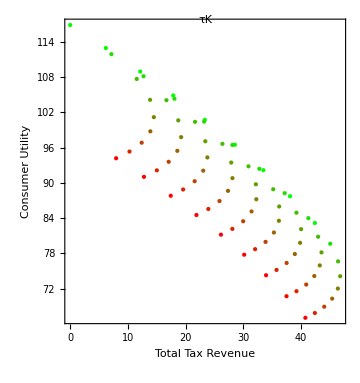
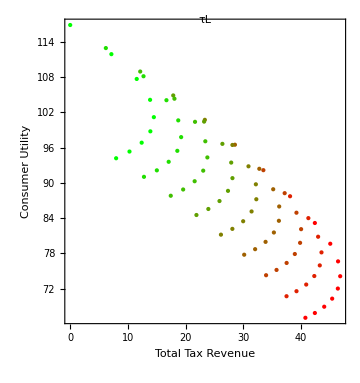
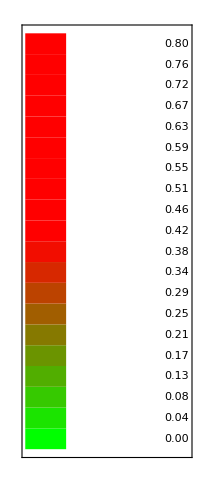
γ= 1/2, η= 1, Borrowinglimit= 0 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
prntcmd
```

```mathematica
time
```

2.10804